```mathematica
A seller values an item at 0. There are n risk neutral bidders, each bidder knows the value, v they place on item. They assume that F(high)=1, F(low)=0. The probability that someone with value v will win is F(v)^(n-1)
```

```mathematica
Expected payment is probability of winning times payment. 
P(v)== ∫_Low^High wⅆ F^(n-1)(w)== vF^(n-1)(v)-∫_Low^High F^(n-1)(w)ⅆw
```

Expected payment conditional on winning is :

```mathematica
B(v)== (P(v))/(F^(n-1)(v))
```

```mathematica
Which is the expected value of the second highest payment
```

```mathematica
CDF[UniformDistribution[{10,30}]]
```

Function[x,Piecewise[{{1/20 (-10+x), 10≤x≤30}, {1, x>30}, {0, True}}],Listable]

```mathematica
Solve[1/20 (-10+x),x]
```

Solve::naqs: 1/20\ (-10 + x) is not a quantified system of equations and inequalities.

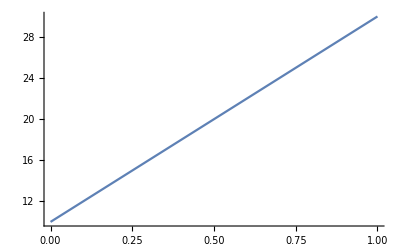

{}

```mathematica
Plot[q(30-10)+10,{q,0,1}]
```

```mathematica
CDF[UniformDistribution[{10,30}],x]
```

Piecewise[{{1/20 (-10+x), 10≤x≤30}, {1, x>30}, {0, True}}]

```mathematica
Solve[1-1/10 (0+x)== q,x]
```

{{x→-10 (-1+q)}}

```mathematica
Solve[1-1/20 (-10+x)== q,x]
```

{{x→-10 (-3+2 q)}}

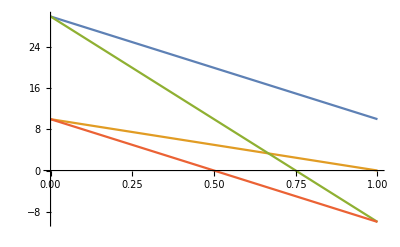

```mathematica
Plot[{-10 (-3+2 q),-10 (-1+q),-20 q-10 (-3+2 q),-10 (-1+q)-10 q},{q,0,1}]
```

```mathematica
D[(-10 (-3+2 q))q,q]
```

-20 q-10 (-3+2 q)

```mathematica
D[(-10 (-1+q))q,q]
```

-10 (-1+q)-10 q